```mathematica
rect[x1_,x2_,y1_,y2_,color_]:=Graphics[{color,Rectangle[{x1,y1},{x2,y2}]},Frame->True,PlotRange->{{0,π/3},{-1,1}}]
```

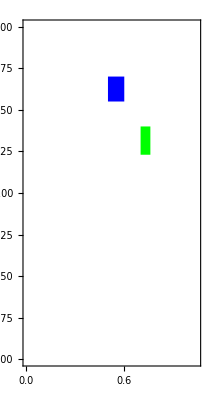

```mathematica
Show[{rect[0.5, 0.6, 0.55, 0.7,Blue],rect[0.7, 0.76, 0.23, 0.4,Green]}]
```

```mathematica
result:=ReadList["/home/kriukov/main/work/mexico/unam/interval-methods/birkhoff.dat",Number,RecordLists->True]
```

```mathematica
(* The belt of 1-2 path with 0.01 tolerance, both clean and unclean rectangles *)
```

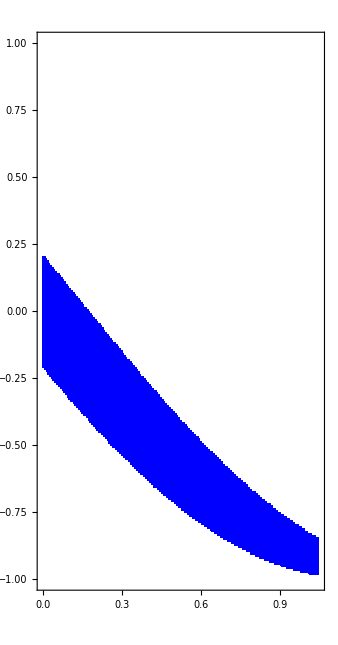

```mathematica
Show[Table[rect[result[[i]][[3]],result[[i]][[4]],result[[i]][[1]],result[[i]][[2]],Blue],{i,Length[result]}]]
```

```mathematica
SetColor[x_]:=Which[x==1,Blue,x==0,Green]
```

```mathematica
(* The belt of 1-2 path with 0.01 tolerance, clean rectangles are blue and unclean are green *)
```

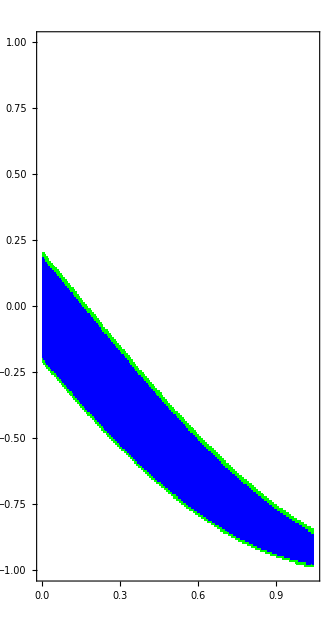

```mathematica
Show[Table[rect[result[[i]][[3]],result[[i]][[4]],result[[i]][[1]],result[[i]][[2]],SetColor[result[[i]][[5]]]],{i,Length[result]}]]
```